```mathematica
u090494e　荒井直幸　2014年10月28日
```

```mathematica
hako[n1_,n2_,l1_,l2_]:=ContourPlot[2/(√(l1 l2)) Sin[(n1 Pi x)/l1] Sin[(n2 Pi y)/l2],{x,0,l1},{y,0,l2},AspectRatio->l2/l1]
```

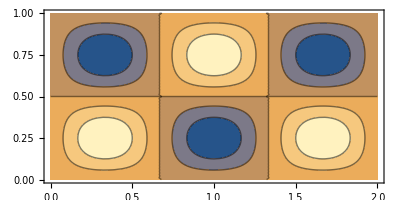

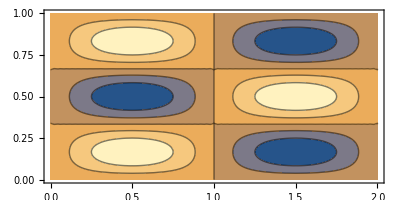

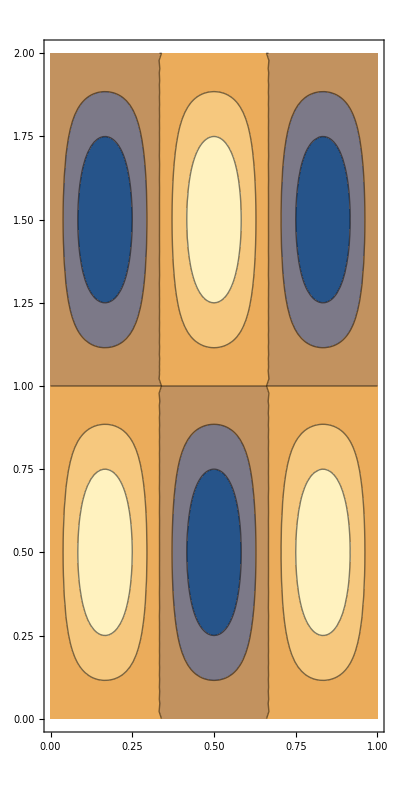

```mathematica
hako[3,2,2,1]
hako[2,3,2,1]
hako[3,2,1,2]
```

```mathematica
課題１
```

```mathematica
L1=L2の時に縮退が起こる。
```

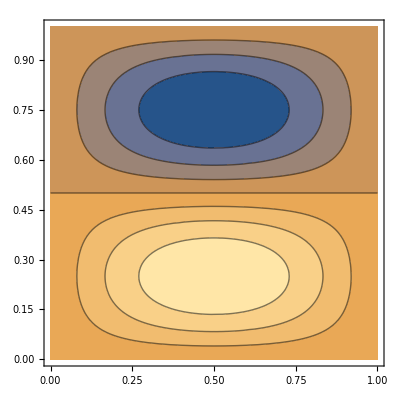

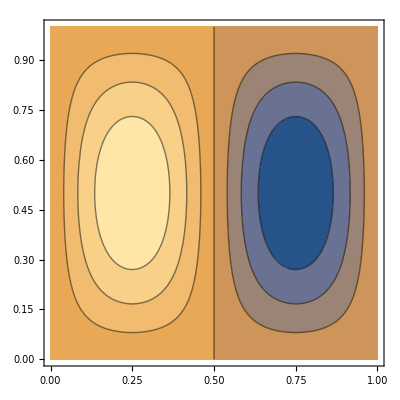

```mathematica
hako[1,2,1,1]
hako[2,1,1,1]
```

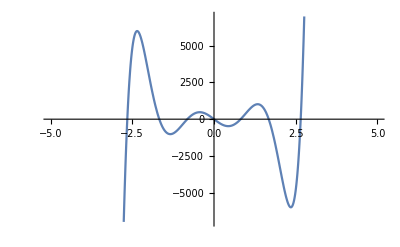

```mathematica
Plot[HermiteH[7,x],{x,-5,5},PlotRange->{-7000,7000}]
```

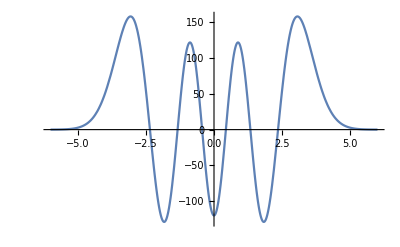

```mathematica
Plot[HermiteH[6,x] Exp[-x^2/2],{x,-6,6},PlotRange->All]
```

```mathematica
課題２
```

```mathematica
f1=Plot[x^2,{x,-1,10},PlotRange->{0,1},PlotStyle->{RGBColor[0,1,0]}];
f2=Plot[(1-Exp[-x])^2,{x,-1,10},PlotRange->{0,1},PlotStyle->{RGBColor[1,0,0]}];
```

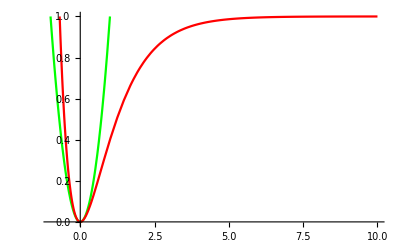

```mathematica
Show[f1,f2]
```

```mathematica
SphericalPlot3D[Abs[SphericalHarmonicY[1,1,theta,phi]]^2,{theta,0,Pi},{phi,0,2Pi}]
```

-Graphics3D-

```mathematica
課題３
```

```mathematica
g1=SphericalPlot3D[Abs[SphericalHarmonicY[2,-2,theta,phi]]^2,{theta,0,Pi},{phi,0,2Pi}]
g2=SphericalPlot3D[Abs[SphericalHarmonicY[2,-1,theta,phi]]^2,{theta,0,Pi},{phi,0,2Pi}]
g3=SphericalPlot3D[Abs[SphericalHarmonicY[2,0,theta,phi]]^2,{theta,0,Pi},{phi,0,2Pi}]
g4=SphericalPlot3D[Abs[SphericalHarmonicY[2,1,theta,phi]]^2,{theta,0,Pi},{phi,0,2Pi}]
g5=SphericalPlot3D[Abs[SphericalHarmonicY[2,2,theta,phi]]^2,{theta,0,Pi},{phi,0,2Pi}]
Show[g1,g2,g3,g4,g5,PlotRange->{{-0.2,0.2},{-0.2,0.2},{-0.4,0.4}}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»

```mathematica
R[n_,l_,x_]:=√(((2/n)^3 (n-l-1)!)/(2 n (n+1)!)) ((2 x)/n)^l ⅇ^(-x/n) LaguerreL[n-l-1,2l+1,(2 x)/n]
```

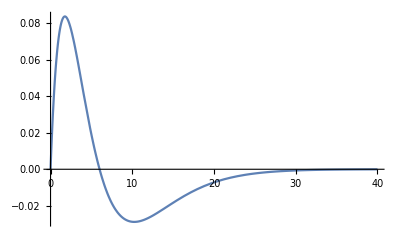

```mathematica
Plot[R[3,1,x],{x,0,40},PlotRange->All]
```

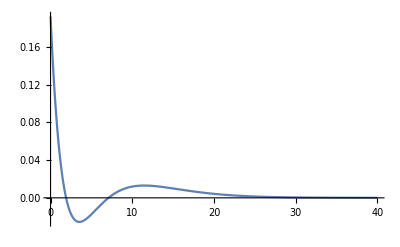
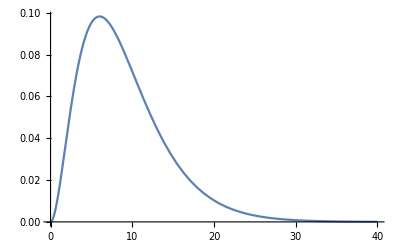
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Plot[R[3,l,x],{x,0,40},PlotRange->All],{l,0,2}]
```

```mathematica
SphericalPlot3D[Abs[SphericalHarmonicY[0,0,theta,phi]]^2,{theta,0,Pi},{phi,0,2Pi}]
```

-Graphics3D-

```mathematica
SphericalPlot3D[Abs[SphericalHarmonicY[1,0,theta,phi]]^2,{theta,0,Pi},{phi,0,2Pi}]
```

-Graphics3D-

```mathematica
SphericalPlot3D[Abs[-SphericalHarmonicY[1,1,theta,phi]+SphericalHarmonicY[1,-1,theta,phi]]^2/2,{theta,0,Pi},{phi,0,2Pi},PlotRange->All]
```

-Graphics3D-

```mathematica
SphericalPlot3D[Abs[SphericalHarmonicY[1,1,theta,phi]+SphericalHarmonicY[1,-1,theta,phi]]^2/2,{theta,0,Pi},{phi,0,2Pi},PlotRange->All]
```

-Graphics3D-

```mathematica
課題４
```

```mathematica
h1=SphericalPlot3D[Abs[-SphericalHarmonicY[2,1,theta,phi]+SphericalHarmonicY[2,-1,theta,phi]]^2/2,{theta,0,Pi},{phi,0,2Pi},PlotRange->All]
h2=SphericalPlot3D[Abs[SphericalHarmonicY[2,1,theta,phi]+SphericalHarmonicY[2,-1,theta,phi]]^2/2,{theta,0,Pi},{phi,0,2Pi},PlotRange->All]
h3=SphericalPlot3D[Abs[-SphericalHarmonicY[2,2,theta,phi]+SphericalHarmonicY[2,-2,theta,phi]]^2/2,{theta,0,Pi},{phi,0,2Pi},PlotRange->All]
h4=SphericalPlot3D[Abs[SphericalHarmonicY[2,2,theta,phi]+SphericalHarmonicY[2,-2,theta,phi]]^2/2,{theta,0,Pi},{phi,0,2Pi},PlotRange->All]
h5=SphericalPlot3D[Abs[SphericalHarmonicY[2,0,theta,phi]+SphericalHarmonicY[2,0,theta,phi]]^2/2,{theta,0,Pi},{phi,0,2Pi},PlotRange->All]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«2 more identical outputs»